```mathematica
(*This code is supposed to calculate u and A for the case κ=1/(√2). The system of equations are described as self dual. We want to find the closed form solution near this point.
It is worth noting that perturbation is supposed to capture this according to the paper "ASYMPTOTIC ANALYSIS OF THE ONE-DIMENSIONAL GINZBURG-LANDAU EQUATIONS NEAR SELF-DUALITY"-Y Amalog*)
```

```mathematica
ClearAll["Global`*"]
```

{{ψ[x]→InterpolatingFunction[…][x],A[x]→InterpolatingFunction[…][x]}}

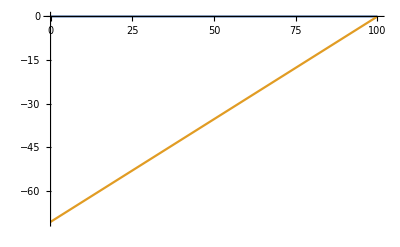

```mathematica
(*For κ=1/(√2), we have the following equations.*)
eqn1:=Sqrt[2]*A'[x]-1+ψ[x]^2
eqn2:=Sqrt[2]*ψ'[x]+ψ[x]*A[x]
L=100;
ψ0=0.4;
H=1/Sqrt[2];
sol=NDSolve[{Sqrt[2]*A'[x]-1+ψ[x]^2==0,Sqrt[2]*ψ'[x]+ψ[x]*A[x]==0,ψ'[L]==0,A'[L]==H},{ψ[x],A[x]},{x,0,L}](*,Method->Reduce*)
(*sol=NDSolve[{Sqrt[2]*A'[x]-1+ψ[x]^2==0,Sqrt[2]*ψ'[x]+ψ[x]*A[x]==0,ψ[L]==ψ0,A'[L]==H},{ψ[x],A[x]},{x,0,L}];*)
Plot[{ψ[x]/. sol,A[x]/. sol},{x,0,L}]
(*NDSolve can only pick up the Normal phase, but not the other phases.*)
```

```mathematica
(*Checking to see what the solution of integration looks like*)
Manipulate[Plot[{x,Re[NIntegrate[1/(Sqrt[2]*t*Sqrt[t-c-Log[t]]),{t,Min[R^2,q^2],Max[R^2,q^2]},MaxRecursion->100]],Im[NIntegrate[1/(Sqrt[2]*t*Sqrt[t-c-Log[t]]),{t,Min[R^2,q^2],Max[R^2,q^2]},MaxRecursion->100]]},{q,0,1.5},PlotRange->{-10,10},PlotLegends->{"x","Re[]","Im[]"}],{R,0,2},{{c,1},0,2},{{x,1},0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
(*The paper by Amalog goves a cl;osed form solution to the Self dual problem.*)
f[q_?NumericQ,c_?NumericQ,q0_?NumericQ]:=NIntegrate[-1/(Sqrt[2]*t*Sqrt[t-c-Log[t]]),{t,q0^2,q^2}]
(*Manipulate[NIntegrate[-1/(Sqrt[2]*t*Sqrt[t-0.1-Log[t]]),{t,0.4,q^2}],{q,0,1}]*)
(*Reduce[f[q]==0&&0<q<1,q]*)
(*Manipulate[Solve[x==NIntegrate[-1/(Sqrt[2]*t*Sqrt[t-c-Log[t]]),{t,ψ0^2,ψ^2}],ψ],{x,0,L},{c,1,10}]*)
(*Manipulate[FindRoot[f[q,c,q0]==x,{q,0.1}],{x,0,L},{c,1.1,10},{q0,0,1}]*)
Manipulate[FindRoot[f[q,c,q0]==x,{q,0.4}],{x,0,L},{c,1,10},{q0,0,1}]
```

FindRoot::nlnum: The function value {f[0.4,1.,0.]} is not a list of numbers with dimensions {1} at {q} = {0.4}.

```mathematica
(*(*Solving for ψ[x]Nunmerically*)
N=100;
Δx=L/N;
For[x=0,x<=L,x=x+Δx,body]*)
```

```mathematica
Manipulate[Plot[1/(Sqrt[2]*x*Sqrt[x-c-Log[x]]),{x,0,2},PlotRange->{{0,2},{0,10}}],{c,0,10}]
Manipulate[Plot[Sqrt[x-c-Log[x]],{x,0,2},PlotRange->{{0,2},{0,4}}],{c,0,2}]
```